# Combined CFD (CCFD) Scheme Interior

## GR Research Group

```mathematica
Clear["`*"]
SetDirectory[NotebookDirectory[]];
```

## Where to begin...?

Chu Fan Eq. 2.1 begins with the general CCFD formulation. Recall the regular 1st derivative second order FD vs. the standard fourth order tridiagonal CFD:
	FD: f_i'=(-a_1 f_(i-1)+a_1 f_(i+1))/h
	CFD: α f_(i-1)'+f_i'+α f_(i+1)'=(-a_1 f_(i-1)+a_1 f_(i+1))/h

Note: Chu Fan uses the convention of a_i/(2 i h) rather than the convention of a_i/h for first derivatives and a_i/(i h)^2 rather than a_i/h^2. We originally used the former because that’s what Tyler was using, but then we switched at some point to the latter because that’s what Kim was using. In this notebook, I will be using the Kim notation. It could be helpful to name these conventions for our reference.

We could rewrite the 1st derivative FD and CFD schemes as:
	FD: f_i'=1/h a_1 (f_(i+1)-f_(i-1))
	CFD: f_i'+α (f_(i+1)'+f_(i-1)')=1/h a_1 (f_(i+1)-f_(i-1))
For 2nd derivatives, we similarly have:
	FD: f_i''=1/h^2 a_1 (f_(i+1)+f_(i-1))+1/h^2 s f_i
	CFD: f_i''+α (f_(i+1)''+f_(i-1)'')=1/h^2 s f_i+1/h^2 a_1 (f_(i+1)+f_(i-1))
where s=-2 Σ_i a_i in a general sense.

Personal note: I think, using h as derivative order bookkeeping, it may be helpful to multiply it to the LHS (looking at Chu Fan Eq. 2.1). We would then have, for example:
	CFD1: h [f_i'+α (f_(i+1)'+f_(i-1)')]=a_1 (f_(i+1)-f_(i-1))
	CFD2: h^2 [f_i''+α (f_(i+1)''+f_(i-1)'')]=s f_i+a_1 (f_(i+1)+f_(i-1))

The CCFD method extends the CFD to the coupled system:
	Eq. 1: h f_i'+h α_1 (f_(i+1)'+f_(i-1)')+h^2 β_1 (f_(i+1)''-f_(i-1)'')=a_1 (f_(i+1)-f_(i-1))
	Eq. 2: h^2 f_i''+h^2 α_2 (f_(i+1)''+f_(i-1)'')+h β_2 (f_(i+1)'-f_(i-1)')=s f_i+a_2 (f_(i+1)+f_(i-1))
where s=-2 Σ_i a_(2,i) if the first index is Eq. number and the second index is RHS super/sub-diagonal number.

Question: Why are the coupling terms antisymmetric?
Answer: A couple reasons. First, it allows the correct Taylor series terms to cancel out such that Eq. 1 contains only odd derivatives/powers of h while Eq. 2 contains only even derivatives/powers of h. You might think about adding different coupling terms to the f_(i+1) and f_(i-1) derivatives, but Taylor constraint consistency would probably find that they must be negatives of each other. Next, it also makes the Fourier analysis work out right with the correct powers of the imaginary unit i and also giving the right sine/cosine parity (but I think that might just be a consequence of the first reason). Finally, there might be some intuition in it, thinking about the coupling terms as corrections to the remainder terms from a derivative approximation.

If we were to extend to the third derivative method, I think it would be:
	Eq. 1: ?=a_1 (f_(i+1)-f_(i-1))
	Eq. 2: ?=s f_i+a_2 (f_(i+1)-f_(i-1))
	Eq. 3: ?=?

Question: Chu Fan + Eric claims that we can get an 8th order CCFD with only stencil points f_i, f_(i+1), and f_(i-1) by using a third derivative as I was going to try to explain above. However, even the explicit FD 3rd derivative uses 5 grid points ( see https://en.wikipedia.org/wiki/Finite_difference_coefficient ), so how would we be able to generalize the RHS of the CCFD to third derivative while maintaining only 3 stencil points? I think it was suggested that they look at this in Appendix 2 of Chu Fan, but I am still skeptical.
Answer: That’s right, the RHS would have to use 5 stencil points, but the point is that we could get 8th (10th?) order by using a 3rd derivative and third equation, we could maintain a 3-point stencil on the LHS, keeping the triple-tridiagonal structure (which is good for matrix inversion purposes). Thoughts on extending the scheme to be twin-pentadiagonal or maybe triple-pentadiagonal on the LHS with a 5-point RHS. Could get insanely high nominal order, or sacrifice some of those parameters for spectral optimization, but stability is then a major concern.

## Solve the System in Section 2.2

Note: By a “local Hermitian polynomial,” it seems the authors intend to mean a polynomial with Hermite interpolation, or an interpolation polynomial whose conditions are similar to the one used in Kim24.

The derivation from Eq. 2.2 through Eq. 2.8 solves for the sixth-order CCFD coefficients, which are {α_1,β_1,a_1,α_2,β_2,a_2}.

Question: I have not done very much with deriving truncation error for our schemes. Could we review this with a simple example, maybe with the 1st derivative A4 scheme? Might be able to incorporate it algorithmically into our notebooks as a metric of “goodness” for the schemes we generate. Maybe we just want to be able to replicate Table 1, and maybe this is a place where Claude could help appropriately.
Answer: To compute the truncation order, just take the Taylor constraint equations beyond constraining order and plug in the coefficients from up to constraining order.

Let’s do this for i=1, which should be the first interior node (since we are just using the grid points i, i-1, and i+1).

Okay so similar to our Kim24 approach, I’ve set up the matrix system M h⃗=f⃗. In equation form, our equations should be:
	f_0 (or f_(i-1))=H(0)
f_1 (or f_i)=H(1)
f_2 (or f_(i+1))=H(2)
f_0' (or f_(i-1)')=H'(0)
f_2' (or f_(i+1)')=H'(2)
f_0'' (or f_(i-1)'')=H''(0)
f_2'' (or f_(i+1)'')=H''(2)
Using:
	H(x_i)=h_0+h_1 x_i+h_2 x_i^2+h_3 x_i^3+h_4 x_i^4+h_5 x_i^5+h_6 x_i^6=(Σ^6)_(j=0) h_j x^j
H'(x_i)=h_1+2 h_2 x_i+3 h_3 x_i^2+4 h_4 x_i^3+5 h_5 x_i^4+6 h_6 x_i^5=(Σ^6)_(j=0) j h_j x^(j-1)
H''(x_i)=2 h_2+6 h_3 x_i+12 h_4 x_i^2+20 h_5 x_i^3+30 h_6 x_i^4=(Σ^6)_(j=0) j (j-1) h_j x^(j-2)
Then we have:
	H(0)=h_0
H(1)=(Σ^6)_(j=0) h_j
H(2)=(Σ^6)_(j=0) 2^j h_j
H'(0)=h_1
H'(2)=(Σ^6)_(j=1) j 2^(j-1) h_j
H''(0)=2 h_2
H''(2)=(Σ^6)_(j=2) j (j-1) 2^(j-2) h_j

```mathematica
fOrder=3;
fpOrder=2;
fppOrder=2;
PolynomialOrder=fOrder+fpOrder+fppOrder-1;

(*Note: Mathematica doesn't like 0^0 but here it is helpful that 0^0=1*)
MMat={{1(*0^0*),0^1,0^2,0^3,0^4,0^5,0^6},{1^0,1^1,1^2,1^3,1^4,1^5,1^6},{2^0,2^1,2^2,2^3,2^4,2^5,2^6},{0,1,0,0,0,0,0},{0,1*2^(1-1),2*2^(2-1),3*2^(3-1),4*2^(4-1),5*2^(5-1),6*2^(6-1)},{0,0,2,0,0,0,0},{0,0,2*1*2^(2-2),3*2*2^(3-2),4*3*2^(4-2),5*4*2^(5-2),6*5*2^(6-2)}};
hVec=Table[ToExpression[StringJoin["h",ToString[i]]],{i,0,PolynomialOrder}]
fVec={f0,f1,f2,fp0,fp2,fpp0,fpp2} (*As in Eq. 2.2, we do NOT include Subscript[f, 1]' or Subscript[f, 1]'', which are Subscript[f, i]' and Subscript[f, i]'', since they are coefficients in Eq. 3 I think.*)


H[x_]=Total[Table[hVec[[i+1]]*x^i,{i,0,PolynomialOrder}]]
Hp[x_]=D[H[x],x]
Hpp[x_]=D[H[x],{x,2}]

(*Eq22={H[i-1]==fim1,H[i]==fi,H[i+1]==fip1,Hp[i-1]==fpim1,Hp[i+1]==fpip1,Hpp[i-1]==fppim1,Hpp[i+1]==fppip1};
Eq22//TableForm*)
Print["System:\n",MatrixForm[MMat]," ",MatrixForm[hVec]," = ",MatrixForm[fVec]]

hCoeffs=Solve[MMat.hVec==fVec,hVec][[1]];
Print["Solution:\n",MatrixForm[hCoeffs]]
```

{h0,h1,h2,h3,h4,h5,h6}

{f0,f1,f2,fp0,fp2,fpp0,fpp2}

h0+h1 x+h2 x^2+h3 x^3+h4 x^4+h5 x^5+h6 x^6

h1+2 h2 x+3 h3 x^2+4 h4 x^3+5 h5 x^4+6 h6 x^5

2 h2+6 h3 x+12 h4 x^2+20 h5 x^3+30 h6 x^4

System:
(1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 2 | 4 | 8 | 16 | 32 | 64
0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 4 | 12 | 32 | 80 | 192
0 | 0 | 2 | 0 | 0 | 0 | 0
0 | 0 | 2 | 12 | 48 | 160 | 480) (h0
h1
h2
h3
h4
h5
h6) = (f0
f1
f2
fp0
fp2
fpp0
fpp2)

Solution:
(h0→f0
h1→fp0
h2→fpp0/2
h3→1/4 (-21 f0+32 f1-11 f2-16 fp0+6 fp2-5 fpp0-fpp2)
h4→1/16 (111 f0-192 f1+81 f2+76 fp0-46 fp2+18 fpp0+8 fpp2)
h5→1/16 (-51 f0+96 f1-45 f2-33 fp0+27 fp2-7 fpp0-5 fpp2)
h6→1/16 (8 f0-16 f1+8 f2+5 fp0-5 fp2+fpp0+fpp2))

Okay I must admit I’m confused on how to equate this with the CCFD Eq’s in 2.7 and 2.8. Also I feel like we ought to include f_i' and f_i'', it looks like the paper is just being convoluted and doing that separately in Eq. 2.5?


Eq. 2.9 and Eq. 2.10 have the same structure as our A-schemes for 1st and 2nd derivatives (pentadiagonal LHS, septadiagonal RHS).

### Taylor method

I just went on the whiteboard and derived the Taylor eq’s for CCD up to sixth order (up to eighth for truncation).

-Graphics-
(Picture from 2026-05-13)

I also notice that these are technically two uncoupled sets of 3 equations each.

```mathematica
CCFDparams={α1,β1,a1,α2,β2,a2};
CCFDeqs={
(*𝒪(h^1)*)1+2 α1==2 a1,
(*𝒪(h^2)*)1+2 α2+2 β2==1/(2!) 2 a2,
(*𝒪(h^3)*)1/(2!) 2 α1+2 β1==1/(3!) 2 a1,
(*𝒪(h^4)*)1/(2!) 2 α2+1/(3!) 2 β2==1/(4!) 2 a2,
(*𝒪(h^5)*)1/(4!) 2 α1+1/(3!) 2 β1==1/(5!) 2 a1,
(*𝒪(h^6)*)1/(4!) 2 α2+1/(5!) 2 β2==1/(6!) 2 a2
};

CCFDcoeff=Solve[CCFDeqs,CCFDparams][[1]]
```

{α1→7/16,β1→-1/16,a1→15/16,α2→-1/8,β2→9/8,a2→3}

Nice! This is consistent with Chu Fan at the end of Section 2.2, up to the factor of a_(1,BYU)=(a_(1,CF))/2. We also have β_(2,BYU)=(β_(2,CF))/2 which I hadn’t noticed was different with the Chu Fan notation in Eq. 2.1, but it is indeed consistent results.

### Truncation Error

The truncation terms are:
	𝒪(h^7) : 1/(6!)·2 α_1+1/(5!)·2 β_1=1/(7!)·2 a_1
𝒪(h^8) : 1/(6!)·2 α_2+1/(7!)·2 β_2=1/(8!)·2 a_2

```mathematica
Oh7=Abs[1/(6!)*2 α1+1/(5!)*2 β1-1/(7!)*2 a1]/.CCFDcoeff//N
Oh8=Abs[1/(6!)*2 α2+1/(7!)*2 β2-1/(8!)*2 a2]/.CCFDcoeff//N
```

0.000198413

0.0000496032

The second one matches Chu Fan, the first one doesn’t quite. I dunno, I might have a typo or maybe they did.

## Spectral Analysis

Now we’re into Section 3 of the paper where we perform a Fourier analysis and generate the dispersion relations for the CCFD schemes. As a notational aside, the Chu Fan paper is using ω'(ω) and ω''(ω) for the 1st and 2nd derivative dispersion relations, and we will be using κ̄(κ):=ω'(ω) and κ̃(κ):=(ω''(ω))^2.

I find myself confused as to why they listed Eq. 3.4 through Eq. 3.14. But for the sake of generality, let’s say we have the CCFD equations:
	Eq. 1: h f_i'+h α_1 (f_(i+1)'+f_(i-1)')+h^2 β_1 (f_(i+1)''-f_(i-1)'')=a_1 (f_(i+1)-f_(i-1))
	Eq. 2: h^2 f_i''+h^2 α_2 (f_(i+1)''+f_(i-1)'')+h β_2 (f_(i+1)'-f_(i-1)')=s f_i+a_2 (f_(i+1)+f_(i-1))
And let’s assume we have solved for the interior coefficients {α_1,β_1,a_1,α_2,β_2,a_2}.

Note: I think it’s worth going through this more carefully on a whiteboard as you did in your 2025-05-20 research notes, at least for the sake of correct bookkeeping of the h and h^2 factors. Also refer to 2025-07-11 for 2nd derivatives.

Upon Fourier transforming, I think we will find (note, I think I have to use different f functions in each line or for different derivative orders):
	Eq. 1: k h OverTilde[f̄](k) [1+2 α_1 cos(k h)+2 h β_1 sin(k h)]=f̃(k) [2 a_1 sin(k h)]
	Eq. 2: k h OverTilde[f̄](k) [h+2 h α_2 cos(k h)+2 β_2 sin(k h)]=f̃(k) [4 a_2 sin^2((k h)/2)]

Recall that Chu Fan find:
	α_1=7/16,  β_1=-1/16,  a_1=15/8,  α_2=-1/8,  β_2=9/4,  a_2=3
but also that in our notation we would have a_(1,BYU)=2 a_(1,CF)=15/4 (I think? Might have gone the wrong way with the factor of 2).

So far the derivation is close, aside from negative signs, factors of two, and being careful with factors of k, h, and f. Anyways from here, we could rewrite the system in terms of κ̄(κ) and κ̃(κ) and then solve this system of two equations for both dispersion relations at once, arriving at Eq. 3.17 and Eq. 3.18 in the Chu Fan paper.

I have the tools for spectral analysis and plotting, including the polar and spherical phase speed anisotropy (Eq. 3.19), coded up in another notebook.

### Derivation on the whiteboard

I did the Fourier analysis on the whiteboard.

-Graphics-
(Picture from 2026-05-13)

The key results are:
	κ̄(κ)=(2 a_1 sin(κ))/(1+2 α_1 cos(κ)-κ·2 β_1 sin(κ))
κ̃(κ)=(2 a_2 sin^2(κ/2))/(1+2 α_2 cos(κ)+1/κ·2 β_2 sin(κ))
What I find interesting is that the coupling terms in the denominator have κ-dependence outside of the trigonometric functions, which is different than before. I would be worried about getting singular behavior in the second equation around κ->0, but technically it turns into a sinc(κ) dependence which is well-behaved there. Am I sure this is the right thing to do though? It is different from the Chu Fan approach where κ̄ and κ̃ were solved from a coupled system. Let’s plot what I’ve got.

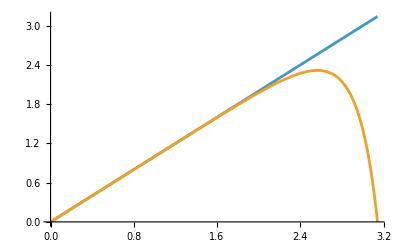

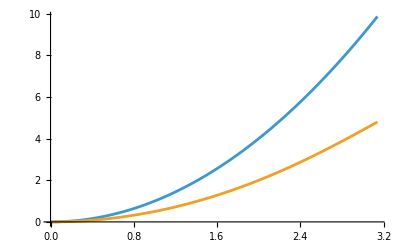

```mathematica
κBarCCFD[κ_]=(2 a1 Sin[κ])/(1+2 α1 Cos[κ]-κ*2 β1 Sin[κ])/.CCFDcoeff;
κTildeCCFD[κ_]=(2 a2 (Sin[κ/2])^2)/(1+2 α2 Cos[κ]+1/κ*2 β2 Sin[κ])/.CCFDcoeff;

Plot[{κ,κBarCCFD[κ]},{κ,0,π}]
Plot[{κ^2,κTildeCCFD[κ]},{κ,0,π}]
```

I guess that’s something, but these are pretty underwhelming. Maybe they do have the incorrect scaling or it’s just the wrong approach. Here is replicating Fig. 1a-b from Chu Fan using their coefficients and equations exactly.

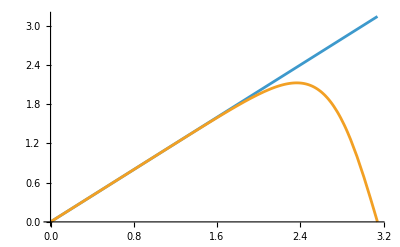

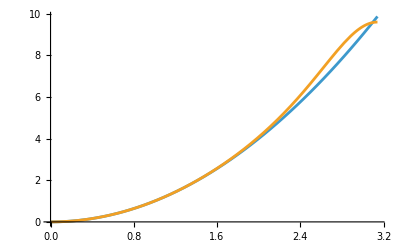

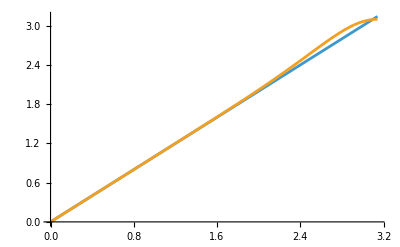

```mathematica
κBarCF[κ_]=(9 Sin[κ] (4+Cos[κ]))/(24+20 Cos[κ]+Cos[2 κ]);
κTildeCF[κ_]=(81-48 Cos[κ]-33 Cos[2 κ])/(48+40 Cos[κ]+2 Cos[2 κ]);

Plot[{κ,κBarCF[κ]},{κ,0,π}]
Plot[{κ^2,κTildeCF[κ]},{κ,0,π}]
Plot[{κ,Sqrt[κTildeCF[κ]]},{κ,0,π}]
```

Note the second two plots are the same, just quadratic vs. linear scaling. Honestly I think my first derivative looks better (I should check numerically with an error measure) but their second derivative looks better. Both are underwhelming, probably because they are nominally 6th order with no spectral optimization, but we could compare this with a few different things as in the Chu Fan plots.

Okay, after meeting with Eric I understand what I did wrong. I’d like to write briefly how he helped me understand this because I thought it was very insightful.
Recall the simplest FD problem:
	f_i'=1/(2h) (f_(i+1)-f_(i-1))
This is actually incorrect; to fix it, we either use an approximation sign ≈ or add a truncation order term:
	f_i'=1/(2h) (f_(i+1)-f_(i-1))+𝒪(h^2)
However, this truncation order term is still hiding information. We can instead write 𝒪(h^2)=R(x;h), where this is a remainder term dependent on x and h. Our FD scheme is then:
	f'(x)=1/(2h) (f(x+h)-f(x-h))+R(x;h)
which we can rewrite as:
	-R(x;h)+f'(x)=1/(2h) (f(x+h)-f(x-h))
-R+f_i'=1/(2h) (f_(i+1)-f_(i-1))
We then define f̄ to be the function such that f̄'=-R+f'. Then, upon Fourier transforming, we will find OverHat[f̄]=f̂ (terms), leading us to our usual dispersion/dissipation relations. In this form it kind of makes why the coupling terms from CCFD give higher order convergence and why we put them on the LHS; they are essentially the leading-order pieces of the remainder function R.

So then to do the Fourier analysis correctly with CCFDs, on the LHS we ought to replace f_i' with (f̄)_i' and f_i'' with (f̃)_i''. This is what will properly introduce the coupling between κ̄ and κ̃ that Chu Fan have. Below is the corrected derivation.

-Graphics-
(Picture from 2026-05-13)

Thus, the correct spectral functions for this CCFD interior are solved by the coupled system:
	κ̄(κ) (1+2 α_1 cos(κ))-κ̃(κ) (2 β_1 sin(κ))=2 a_1 sin(κ)
κ̃(κ) (1+2 α_2 cos(κ))+κ̄(κ) (2 β_2 sin(κ))=4 a_2 sin^2(κ/2)
I verified that this all matches with Chu Fan Eq. 3.15-18, although there definitely is a typo with the bracket in Eq. 3.15.

```mathematica
eq1=κBar (1+2 α1 Cos[κ])-κTilde (2 β1 Sin[κ])==2 a1 Sin[κ];
eq2=κTilde (1+2 α2 Cos[κ])+κBar (2 β2 Sin[κ])==4 a2 (Sin[κ/2])^2;

Solve[{eq1,eq2},{κBar,κTilde}][[1]]/.CCFDcoeff//FullSimplify

κBarCCFD[κ_]=(9 (4+Cos[κ]) Sin[κ])/(24+20 Cos[κ]+Cos[2 κ]);
κTildeCCFD[κ_]=(6 (19+11 Cos[κ]) Sin[κ/2]^2)/(24+20 Cos[κ]+Cos[2 κ]);

Plot[{κ,κBarCCFD[κ]},{κ,0,π}]
Plot[{κ^2,κTildeCCFD[κ]},{κ,0,π}]
Plot[{κ,Sqrt@κTildeCCFD[κ]},{κ,0,π}]
```

{κBar→(9 (4+Cos[κ]) Sin[κ])/(24+20 Cos[κ]+Cos[2 κ]),κTilde→(6 (19+11 Cos[κ]) Sin[κ/2]^2)/(24+20 Cos[κ]+Cos[2 κ])}

-Graphics-

-Graphics-

-Graphics-

## Boundary Closure

We next move into Section 4.1 of the Chu Fan paper. Since we are just using grid points i, i-1, and i+1, we will only have a single boundary row (node 0 and node N).

They seem to just use a shifted-stencil version of the same CCFD approach, which makes sense. Our boundary node 0 equations then are (with i=0):
	Eq. 1: h f_i'+h α_1 f_(i+1)'+h^2 β_1 f_(i+1)''=a_(1,i) f_i+a_(1,i+1) f_(i+1)+a_(1,i+2) f_(i+2)
	Eq. 2: h^2 f_i''+h^2 α_2 f_(i+1)''+h β_2 f_(i+1)'=a_(2,i) f_i+a_(2,i+1) f_(i+1)+a_(2,i+2) f_(i+2)
Also note, notationally I prefer indexing the RHS coefficients as a_(i,j) rather than using a, b, c as Chu Fan does (I believe Tyler, Lele, and Luke do this alphabetical notation as well).

Note: This one is important, not just notation. Due to the antisymmetry of the derivative coupling terms with β_i, the equation for boundary node N will differ with minus signs, as in Eq. 4.3 and Eq. 4.4 on the LHS. On the RHS of those same equations, we see antisymmetry/symmetry depending on whether the RHS is a 1st or 2nd derivative, as usual.

Once we have set up our boundary closure equations, we solve for the coefficients again. Chu Fan likely does this using their “local Hermitian polynomial” method as in Section 2.2. This would seem similar to the Kim24 boundary closures. However, where all this methodology differs is that all parameters are used for nominal order of accuracy; none yet are free parameters for spectral optimization. So anyways, I think we can be aware at this stage that there are different ways of solving for the interior/boundary coefficients of a scheme depending on if we are doing things nominally with Taylor series, adding extra free parameters to our boundary closure as we have done in the CFD Scheme Coefficients notebook, determining them through spectral optimization, or some hybrid mixture of methods.

They look at the truncation error of their boundary closures. This might be good to do as well if we get something systematic put together for the interiors as mentioned above.

Question: I am confused what they mean by a “global CCFD system” above Eq. 4.5. I am also confused as to the difference between twin-forward and elimination and twin-backward substitution in solving the matrix CCFD system. Perhaps it will make more sense once we write up the matrix structure.

Note: For testing with eigenvalues and such in these Mathematica notebooks, I am not so worried about matrix inversion beyond whatever Mathematica’s Inverse command does by default, especially since I would probably just use matrices of size ~120 at most. I’m sure we have decent matrix inversion methods in Dendro-GR for twin-tridiagonal or triple-tridiagonal systems. How about Luke’s codes? I think he was using sparse arrays in Mathematica and then I don’t know about the 1D BSSN code, but I suppose it would be good to check with him if changing the LHS matrix structure will be a big deal computationally in his tests.

Maybe I ought to spend some time reading and trying to understand the appendices in Chu Fan.

In Section 5, all I am gaining is that they use an extrapolation polynomial on the boundary nodes so that their matrix system is fully twin-tridiagonal, rather than being cut off at the boundaries.

I think that’s about all I’m going to get out of the Chu Fan paper, aside from reading the appendices more closely.

Let’s do the Taylor boundary derivation another time because I don’t want to erase the whiteboards quite yet.

## Matrix Formulation

I think this is essentially the last step and I’m unsure if the paper covers it, maybe the box looking things in the appendices. Actually after this we ought to look at the eigenvalues.


Here are my notes on the Hixon paper:
	Question: Where are all the parts of Eq. 1 coming from? I feel like this could explain the antisymmetry of the derivative coupling terms but I don’t understand where they come from here either.
	Note: I think I can kind of understand the matrix formulation here, but I need to write out an explicit example on a whiteboard.
	Question: Where are the optimization parameters σ_1 and σ_2 coming from in Eq. 5?
	Note: It looks like Eq. 7 solves for the coefficients of the scheme in terms of some spectral optimization parameters, similar to what I mentioned in a comment above. So it would be good to be able to re-derive this to understand the approach. Also Hixon uses yet another different notation, so be careful.
	Note: Adding spectral optimization drops the Chu Fan scheme to 4th order, which makes sense. We might need to consider in the future what extensions we can make to these CCFD stencils. For example, if we do the 8th order CCFD with 3rd derivatives, we could drop it to 6th order and have some spectral optimization. Or could we do a twin-pentadiagonal approach? Or increase the RHS stencil size? We should figure out what our limitations are on making new families of CCFDs.
	Question: How do dispersion and dissipation interplay in the CCFDs? Is it correct to say that our κ̄(κ) for 1st derivatives is a dispersion relation and our κ̃(κ) for 2nd derivatives is a dissipation relation, rather than loosely calling them both dispersion relations as I have been?
	Note: I just had to comment, his notation is awful, especially around Eq. 17. I believe that the multi-line parentheticals are just long equations that he didn’t want to write horizontally?
	Note: Interesting optimization approaches; optimize 1st derivative dispersion, optimize 2nd derivative dissipation, optimize both. Sort of similar to the Re/Im/Norm approaches we considered for the CFD boundary optimizations with ŷ? But technically different? I guess I’m not understanding how the Re/Im dispersion/dissipation of boundary stencils is different from the 1st/2nd derivative dispersion/dissipation of CCFD interior stencils.
	Note: Figure 2, now that I understand it, actually does demonstrate pretty well the tradeoff between these different optimization techniques.
	Note: Hixon did the optimization of his spectral parameters with a “brute force” grid search approach; could we do better by defining a spectral error functional and taking a Kim07 approach? I think this again warrants better understanding of the weighting functions and cutoff wavenumber if we were to do so.
	Note: If I connect Figure 3a back to what I learned from the Chen 2023 paper, being above the solid black line could be indicative of temporal instability. Maybe thinking about 3b then gives us hints on how to think about 2nd derivative instabilities more, or maybe this gives us another thing to test with stability.
	Note: Figure 4 confirms what I think Luke’s recent plots from the 2nd derivative A6 schemes with varying values of cutoff wavenumber was showing; more spectral optimization to decrease spectral error will also decrease convergence order, so I think balance is needed. But where is the balance?
	Note: At least Hixon gives the values of his optimization parameters, so we could test them explicitly if we want to.
	Note: Hixon’s boundary closure is just explicit schemes with some ghost point interpolation, so probably not worth looking into very much. However, the stability plot is interesting (Fig. 9). The 1st derivative advection equation test has an eigenvalue spectrum like we’re used to; we could probably replicate this easily if we replicate the Hixon CCFD scheme. However, the 2nd derivative heat equation tests are interesting; his eigenvalues are all real-negative, so I think that is some confirmation that we have been approaching the 2nd derivative eigenvalues the right way. It might be good to try to replicate this as well because he doesn’t have any outliers and so we had better hope we don’t have any either. We could also test these in evolutions for stability, but it’s probably going to depend a lot on the boundary closure (so if we use non-explicit boundary closures, we’ll naturally have a harder time with stability).


Here are my notes on the Gurarslan paper:
	Note: Using the NCCD scheme from Sengupta. Eq. 13 and Eq. 14 might be helpful in terms of matrix decompositions. No other helpful info I think. I glanced at the Sengupta paper and I don’t see much new, but it seems to have some parts from Chu Fan and Hixon written in what I think is a cleaner way, so I saved it.

## Eigenvalue Analysis

Once we have the matrices in hand we ought to look at the eigenvalues of the resulting matrix. We ought to take proper care with the “eigenvalue-striking” procedure, possibly using the non-Dirichlet probe that Claude has mentioned before. I think the Mahesh paper will be helpful here since it addresses CCFD stability.


Need to read Mahesh and Chu Fan 2000 (I glanced at them and they both seem helpful for CCFD stability, but I need a closer reading)

# Twin-Pentadiagonal CCFD Scheme

We next attempt to extend the CCFD scheme to a 5-point stencil on both sides. The scheme equations are then:
	Eq. 1: h f_i'+h α_(1,1) (f_(i+1)'+f_(i-1)')+β_(1,1) (f_(i+2)'+f_(i-2)')+h^2 α_(1,2) (f_(i+1)''-f_(i-1)'')+h^2 β_(1,2) (f_(i+2)''-f_(i-2)'')=a_(1,1) (f_(i+1)-f_(i-1))+a (f_(i+2)-f_(i-2))
	Eq. 2: h^2 f_i''+h^2 α_2 (f_(i+1)''+f_(i-1)'')+h β_2 (f_(i+1)'-f_(i-1)')=s f_i+a_2 (f_(i+1)+f_(i-1))
A quick word on notation: I am subscripting coefficients now as c_(i,j) (where c∈{α,β,a}). For all coefficients, the subscript i denotes the equation number. In other words, when the coupling parameters are set to zero, the equation reduces to the regular CFD for derivative order i. For the LHS coefficients (c∈{α,β}), the subscript j denotes the derivative order, independent of coupling (maybe this is backwards)?

where s=-2 Σ_i a_(2,i) if the first index is Eq. number and the second index is RHS super/sub-diagonal number.